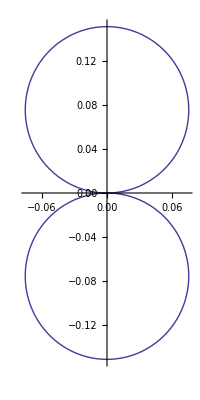

```mathematica
MyPlot = With[{lambda=1},With[{r= 25,k=2 Pi/lambda,eta=120 Pi,I0=1,l=lambda/50},PolarPlot[Abs[Sum[((2n+1)/(n(n+1)))(AmnCoefs[[n]][[n+m+1]]Mfunc[m,n,k,r,thetaValue,0] + BmnCoefs[[n]][[n+m+1]]Nfunc[m,n,k,r,thetaValue,0]),{n,1,numberOfModes},{m,-n,n}]],{thetaValue,-Pi,Pi}]]]
```

```mathematica
Rotate[MyPlot,Pi/2]
```

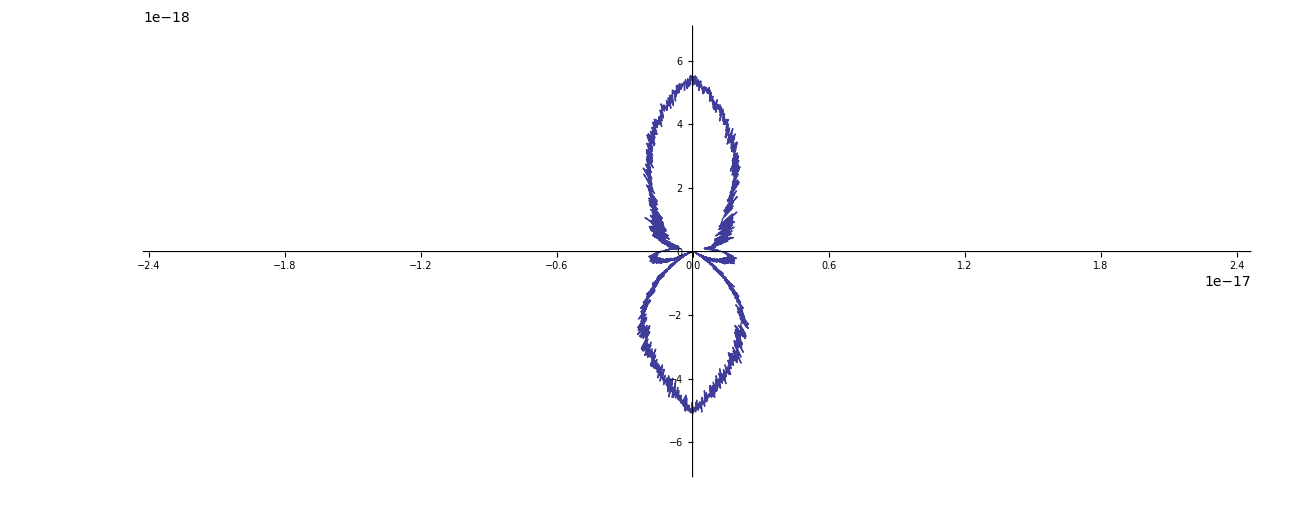

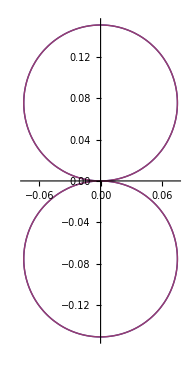

```mathematica
With[{lambda=1},With[{r= 25,k=2 Pi/lambda,eta=120 Pi,I0=1,l=lambda/50},PolarPlot[{Abs[Edipoletheta[r,thetaValue,k,eta,l,I0]],Abs[Sum[((2n+1)/(n(n+1)))(AmnCoefs[[n]][[n+m+1]]Mfunc[m,n,k,r,thetaValue,0] + BmnCoefs[[n]][[n+m+1]]Nfunc[m,n,k,r,thetaValue,0]),{n,1,numberOfModes},{m,-n,n}]]},{thetaValue,-Pi,Pi}]]]
```

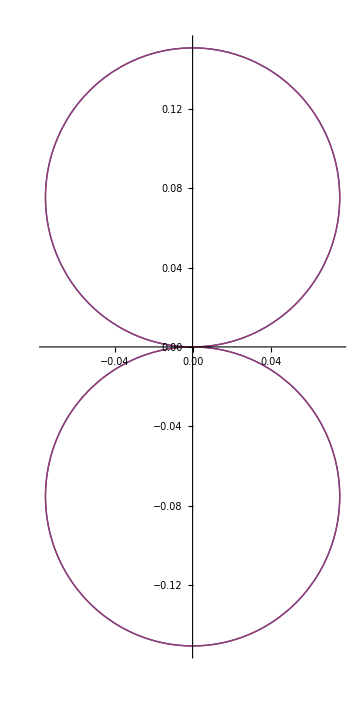

```mathematica
Show[%167,ImageSize->Medium]
```

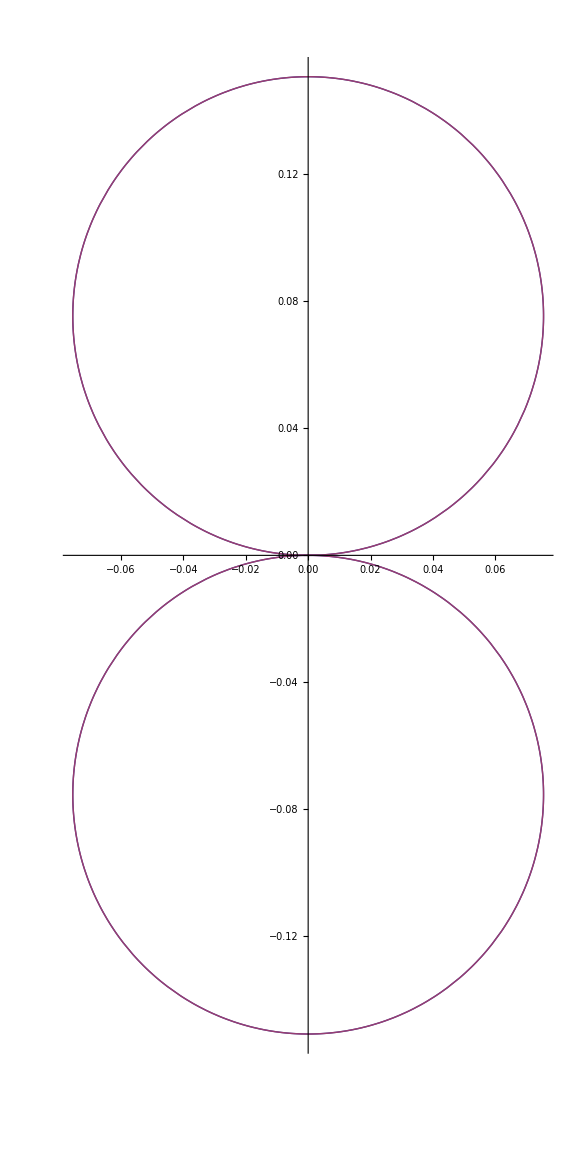

```mathematica
Show[%169,ImageSize->Large]
```

```mathematica
Show[%167,ImageSize->Large]
```

-Graphics-